```mathematica
Clear["Global`*"];
Quit[];
```

# MF superconductor: diagonalization and GS iteration

## This notebook is used for iteration over μ. Everything is defined in corresponding chapters, but the calculation is at the end.

```mathematica
<<sneg`sneg`;
```

sneg 1.250 Copyright (C) 2016 Rok Zitko

Starts with the MF approximation of the superconducting Hamiltonian (where neighbouring levels do not interact). H is diagonalized in Nambu basis. 
In the second part, the operators are applied to their vacuum (0101...01), in order to obtain a ground state. 
In the third part, energy and occupancy number are calculated.

```mathematica
(*Physical parameters*)
n=6; (* number of levels *)
W=1.; (* band [-W:W] *)
ρ=n/(2W); (* density of states *)
spacing=2W/(n+1); (*spacing between energy levels*)
ϵ[i_]:=-W+(2W)/(n+1)i; (* energy levels *)
Δ=0.1; (* initial approximation for Δ. True Δ is determined self-consistently. *)
B=0; (* magnetic field *)
g=0.5/ρ; (* Coupling constant. Note that we keep g*ρ constant, since this combination enters the BCS expression for Δ. *)
h[i_, Δ_,μ_]:={{ϵ[i]-μ+B,Δ},{Δ,-(ϵ[i]-μ)+B}}; (* Hamiltonian block *)
dim=2; (* Dimension of the block *)
zm2=DiagonalMatrix[{0,0}]; (* zero dimxdim matrix *)
matrix[Δ_, μ_]:=ArrayFlatten[Table[If[i==j,h[i, Δ, μ],zm2],{i,n},{j,n}]](* MF Hamiltonian *)
```

## Diagonalization

```mathematica
(* j: state number *)
(* i: level index *)
u[j_,i_]:=vectors[[j,dim(i-1)+1]];
v[j_,i_]:=vectors[[j,dim(i-1)+2]];
```

```mathematica
(*Computing parameters used in the while loop*)
precision = 0.0001;
maxIteration=20;
```

## GS iteration

```mathematica
Off[General::spell1];
snegfermionoperators[c]
```

```mathematica
mybasis = makebasis[Table[c[i],{i, n}]];
```

```mathematica
(*Exact Hamiltonian*)
kinetic=Sum[ϵ[j](nc[c[CR,j,UP ],c[AN,j,UP]]+nc[c[CR,j,DO],c[AN,j,DO]]),{j,n}];
interaction=-g Sum[ nc[nc[c[CR,j,UP],c[CR,j,DO]],nc[c[AN,j,UP],c[AN,j,DO]]],{j,n}];
Hexact = kinetic+interaction
```

-0.714286 (c_(1↓)^†·c_(1↓)^+c_(1⇑)^†·c_(1⇑)^)-0.428571 (c_(2↓)^†·c_(2↓)^+c_(2⇑)^†·c_(2⇑)^)-0.142857 (c_(3↓)^†·c_(3↓)^+c_(3⇑)^†·c_(3⇑)^)+0.142857 (c_(4↓)^†·c_(4↓)^+c_(4⇑)^†·c_(4⇑)^)+0.428571 (c_(5↓)^†·c_(5↓)^+c_(5⇑)^†·c_(5⇑)^)+0.714286 (c_(6↓)^†·c_(6↓)^+c_(6⇑)^†·c_(6⇑)^)-0.166667 (c_(1↓)^†·c_(1⇑)^†·c_(1↓)^·c_(1⇑)^+c_(2↓)^†·c_(2⇑)^†·c_(2↓)^·c_(2⇑)^+c_(3↓)^†·c_(3⇑)^†·c_(3↓)^·c_(3⇑)^+c_(4↓)^†·c_(4⇑)^†·c_(4↓)^·c_(4⇑)^+c_(5↓)^†·c_(5⇑)^†·c_(5↓)^·c_(5⇑)^+c_(6↓)^†·c_(6⇑)^†·c_(6↓)^·c_(6⇑)^)

```mathematica
(*MF Hamiltonian*)
interactionMF= Sum[Δ nc[c[CR,j,UP],c[CR,j,DO]]+ conj[Δ]nc[c[AN,j,DO],c[AN,j,UP]],{j, n}];
HMF = kinetic+interactionMF
```

-0.1 c_(1↓)^†·c_(1⇑)^†-0.714286 (c_(1↓)^†·c_(1↓)^+c_(1⇑)^†·c_(1⇑)^)-0.1 c_(2↓)^†·c_(2⇑)^†-0.428571 (c_(2↓)^†·c_(2↓)^+c_(2⇑)^†·c_(2⇑)^)-0.1 c_(3↓)^†·c_(3⇑)^†-0.142857 (c_(3↓)^†·c_(3↓)^+c_(3⇑)^†·c_(3⇑)^)-0.1 c_(4↓)^†·c_(4⇑)^†+0.142857 (c_(4↓)^†·c_(4↓)^+c_(4⇑)^†·c_(4⇑)^)-0.1 c_(5↓)^†·c_(5⇑)^†+0.428571 (c_(5↓)^†·c_(5↓)^+c_(5⇑)^†·c_(5⇑)^)-0.1 c_(6↓)^†·c_(6⇑)^†+0.714286 (c_(6↓)^†·c_(6↓)^+c_(6⇑)^†·c_(6⇑)^)+0.1 c_(1↓)^·c_(1⇑)^+0.1 c_(2↓)^·c_(2⇑)^+0.1 c_(3↓)^·c_(3⇑)^+0.1 c_(4↓)^·c_(4⇑)^+0.1 c_(5↓)^·c_(5⇑)^+0.1 c_(6↓)^·c_(6⇑)^

```mathematica
(*Initial state*)
V = vc@@Table[(1/2)(1+(-1)^i),{i, 2n}]
```

‖▯▮▯▮▯▮▯▮▯▮▯▮⟩

```mathematica
(*Diagonal operators*)
d[j_]:=Sum[u[j, i]c[CR,i,UP] + v[j, i]c[AN,i,DO],{i,n}]
```

## Occupancy number

```mathematica
(*Occupancy number operators; for each energy level and for the total occupancy*)
Nop[i_] := nc[c[CR, i,  UP],c[AN, i, UP]] + nc[c[CR, i,  DO],c[AN, i, DO]];
NopTotal:=Sum[Nop[i],{i,n}];
```

```mathematica
(*Occupancy number functions; calculate the expected occupancy of a given state*)
Nlevels[state_]:=Table[scalarproductvc[state,ap[Nop[i],state]],{i, n}];
Ntotal[state_]:=scalarproductvc[state,ap[NopTotal,state]];
```

## Loop over μ

```mathematica
μmin=-2spacing;
μmax=2spacing;
dμ=0.5spacing;
```

## Occupancy

### List of lists

```mathematica
(*Calculate the occupancy table for values of μ in the interval (μmin, μmax, dμ).*)
OccupancyTableOfTables=
Flatten[
Reap[
Do[
iteration = 0;
oldΔ = Δ+1;

(*The loop calculates Δ self-consistently*)
While[Abs[(Δ/oldΔ)-1]>precision ∧ iteration<maxIteration,
{energies, vectors} =Transpose[Sort[Transpose[Eigensystem[matrix[Δ, μ]]]]];
oldΔ=Δ;
Δ= Sum[-g u[j,i]v[j,i],{j,n},{i,n}];
iteration++;
];

(*Iteratively construct a list of successive states η. η[i]=d[i-1]d[i-1]...d[1].V*)
η={V};
Do[η=Append[η,ap[d[i],η[[-1]]]],{i, n}];

tabela1=Table[Ntotal[η[[i]]],{i, n+1}];

(*Calculate occupancy and append*)
Sow[tabela1];

,{μ, μmin,μmax, dμ}]][[2]],1]
```

{{5,4.01428,3.03926,2.09297,1.26733,1.26733},{5,4.02613,3.07551,2.19712,2.7195,2.19712},{5,4.04386,3.13521,3.87148,3.13521,3.13521},{5,4.06717,4.908,4.06717,4.52698,4.06717},{5,5.89677,5.,5.71176,5.,5.},{5,5.93281,6.77361,5.93281,6.39256,5.93281},{5,5.95611,6.86471,7.60088,6.86471,6.86471},{5,5.97385,6.92444,7.80276,8.32501,7.80276},{5,5.98571,6.96072,7.90698,8.73253,8.73253}}

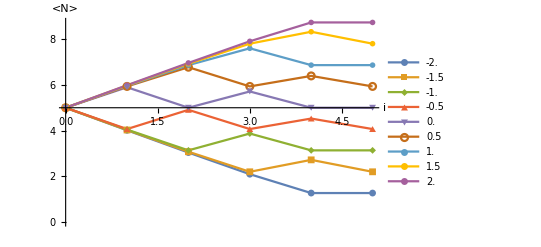

```mathematica
occupancyMu1=ListPlot[OccupancyTableOfTables, 
PlotLegends->Table[μ/spacing,{μ, μmin,μmax,dμ}],DataRange->{0,n},
Joined->True, PlotMarkers->{Automatic,7},AxesLabel->{"i","<N>"}, AxesOrigin->{0,n}]
```

```mathematica
(*Export["occupancy_mu_n5.pdf", occupancyMu1];*)
```

### Value at last step

```mathematica
μmin=-2spacing;
μmax=2spacing;
dμ=0.25spacing;
```

```mathematica
(*Calculate the occupancy in the last step of the iteration for values of μ in the interval (μmin, μmax, dμ).*)
OccupancyTableLastStep=
Flatten[
Reap[
Do[
iteration = 0;
oldΔ = Δ+1;

(*The loop calculates Δ self-consistently*)
While[Abs[(Δ/oldΔ)-1]>precision ∧ iteration<maxIteration,
{energies, vectors} =Transpose[Sort[Transpose[Eigensystem[matrix[Δ, μ]]]]];
oldΔ=Δ;
Δ= Sum[-g u[j,i]v[j,i],{j,n},{i,n}];
iteration++;
];

(*Iteratively construct a list of successive states η. η[i]=d[i-1]d[i-1]...d[1].V*)
η={V};
Do[η=Append[η,ap[d[i],η[[-1]]]],{i, n}];

tabela1=Table[Ntotal[η[[i]]],{i, n+1}];

(*Calculate occupancy and append*)
Sow[tabela1[[-1]]];

,{μ, μmin,μmax, dμ}]][[2]],1]
```

{2.24167,2.70898,3.18521,3.65739,4.12326,4.59045,5.062,5.53294,6.,6.46705,6.93797,7.4095,7.87668,8.34253,8.8147,9.29093,9.75819}

```mathematica
occupancyMu2=ListPlot[OccupancyTableLastStep, DataRange->{μmin, μmax}];
```

```mathematica
predicitionMuPlot=Plot[n+(2 μ/spacing),{μ,μmin, μmax},PlotStyle->{Red, Dashed}];
```

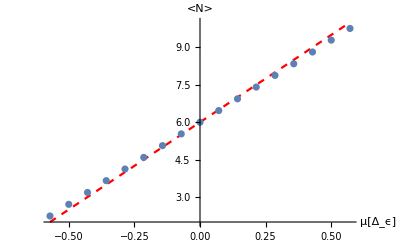

```mathematica
Show[predicitionMuPlot,occupancyMu2,AxesLabel->{"μ[Δ_ϵ]", "<N>"}]
```